```mathematica
Γ=11 (*MHz*);
```

```mathematica
Manipulate[Plot[Exp[-τ*Ωup^2*4*Γ*(-Δdown+Δup)^2/Abs[Ωdown^2+2*I*(-Δdown+Δup)*(Γ+2*I*Δup)]^2],{Δup,-50,50},PlotRange->Full,PlotPoints->10000],{Ωup,0.01,5},{Δdown,-Γ,Γ},{Ωdown,0.01,10},{τ,1,100}]
```

```mathematica
H={{0,Ω12,0},{Ω12,δ,Ω23},{0,Ω23,0}}/.{Ω12->1,Ω23->1};
```

```mathematica
Eigensystem[H]//FullSimplify
```

{{0,1/2 (δ-√(8+δ^2)),1/2 (δ+√(8+δ^2))},{{-1,0,1},{1,1/2 (δ-√(8+δ^2)),1},{1,1/2 (δ+√(8+δ^2)),1}}}

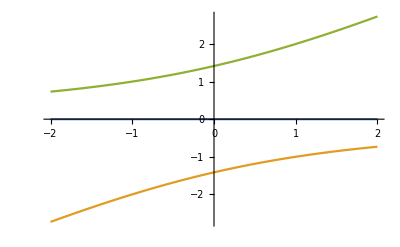

```mathematica
Plot[{0,1/2 (δ-√(8+δ^2)),1/2 (δ+√(8+δ^2))},{δ,-2,2}]
```